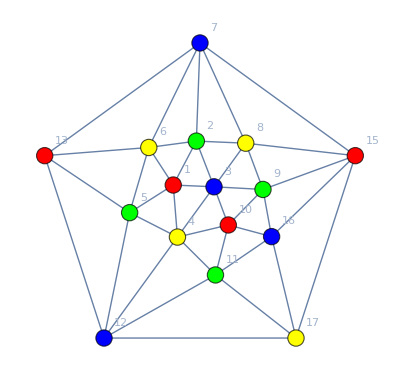
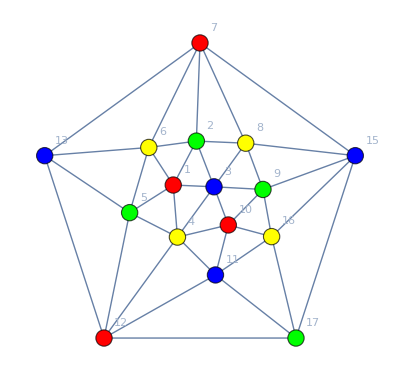
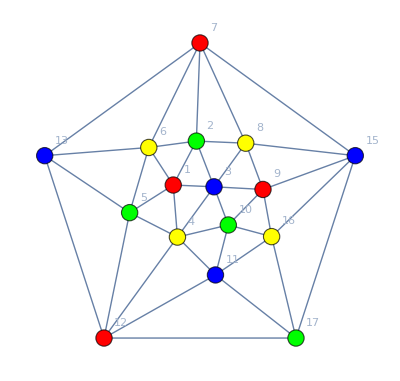
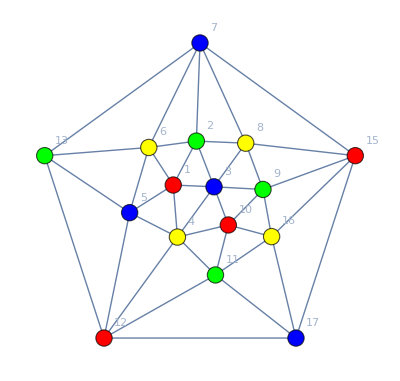
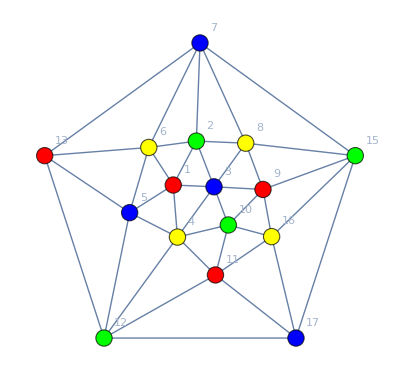
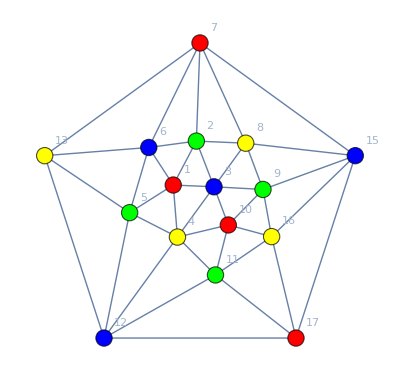
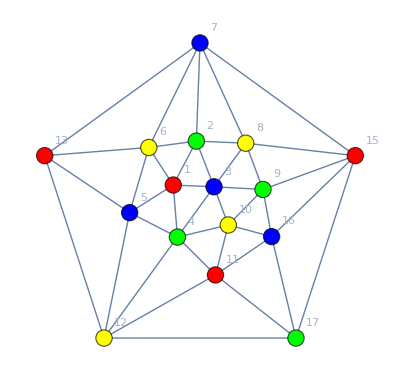
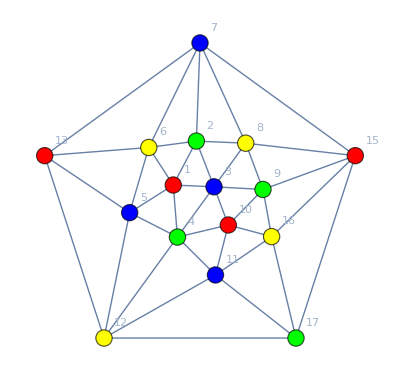
<|7c♁df♁h→{{7c♁df♁h,-Graphics-},{7c♁df♁h,-Graphics-},{7c♁df♁h,-Graphics-}},7h♁cf♁d→{{7h♁cf♁d,-Graphics-},{7h♁cf♁d,-Graphics-},{7h♁cf♁d,-Graphics-}},7♁c♁df♁h→{{7♁c♁df♁h,-Graphics-},{7♁c♁df♁h,-Graphics-},{7♁c♁df♁h,-Graphics-},{7♁c♁df♁h,-Graphics-},{7♁c♁df♁h,-Graphics-},{7♁c♁df♁h,-Graphics-}},7h♁c♁d♁f→{{7h♁c♁d♁f,-Graphics-},{7h♁c♁d♁f,-Graphics-},{7h♁c♁d♁f,-Graphics-},{7h♁c♁d♁f,-Graphics-},{7h♁c♁d♁f,-Graphics-},{7h♁c♁d♁f,-Graphics-}},7♁cf♁dh→{{7♁cf♁dh,-Graphics-},{7♁cf♁dh,-Graphics-},{7♁cf♁dh,-Graphics-},{7♁cf♁dh,-Graphics-},{7♁cf♁dh,-Graphics-},{7♁cf♁dh,-Graphics-},{7♁cf♁dh,-Graphics-},{7♁cf♁dh,-Graphics-}},7c♁dh♁f→{{7c♁dh♁f,-Graphics-},{7c♁dh♁f,-Graphics-},{7c♁dh♁f,-Graphics-},{7c♁dh♁f,-Graphics-},{7c♁dh♁f,-Graphics-},{7c♁dh♁f,-Graphics-},{7c♁dh♁f,-Graphics-},{7c♁dh♁f,-Graphics-}},7♁cf♁d♁h→{{7♁cf♁d♁h,-Graphics-},{7♁cf♁d♁h,-Graphics-},{7♁cf♁d♁h,-Graphics-},{7♁cf♁d♁h,-Graphics-},{7♁cf♁d♁h,-Graphics-},{7♁cf♁d♁h,-Graphics-},{7♁cf♁d♁h,-Graphics-},{7♁cf♁d♁h,-Graphics-},{7♁cf♁d♁h,-Graphics-}},7c♁d♁f♁h→{{7c♁d♁f♁h,-Graphics-},{7c♁d♁f♁h,-Graphics-},{7c♁d♁f♁h,-Graphics-},{7c♁d♁f♁h,-Graphics-},{7c♁d♁f♁h,-Graphics-},{7c♁d♁f♁h,-Graphics-},{7c♁d♁f♁h,-Graphics-},{7c♁d♁f♁h,-Graphics-},{7c♁d♁f♁h,-Graphics-}},7♁c♁dh♁f→{{7♁c♁dh♁f,-Graphics-},{7♁c♁dh♁f,-Graphics-},{7♁c♁dh♁f,-Graphics-},{7♁c♁dh♁f,-Graphics-},{7♁c♁dh♁f,-Graphics-},{7♁c♁dh♁f,-Graphics-},{7♁c♁dh♁f,-Graphics-},{7♁c♁dh♁f,-Graphics-},{7♁c♁dh♁f,-Graphics-},{7♁c♁dh♁f,-Graphics-},{7♁c♁dh♁f,-Graphics-}}|>

```mathematica
With[{g=Graph[EmbedGraphInPlantri8[allGraphs5,lambdaKey],VertexLabels->"Name",GraphLayout->"TutteEmbedding"]},
GroupBy[Map[{With[{s=SetsToSymbol[SymbolToSets[FilterSymbol[#,{12,13,7,15,17}]]]},SymbolToLabel[s]],ColorGraph[g,SymbolToSets[#]]}&,FindFullFormula4[ g]],First]//Sort
]
```

```mathematica
FilterSymbol2[sym_,vertices_]:=Block[{v2=SymbolToSets[sym]},
v2=Map[Select[#,!MemberQ[vertices,#]&]&,v2];
v2=Select[v2,#≠{}&];
v2=Sort[Map[Sort[#]&,v2],#1[[1]]<#2[[1]]&];
Simplify[SetsToSymbol[v2]]
]
```

```mathematica
TableForm[Map[{First[#],DeleteDuplicates[Map[Last,#[[2]]]]}&,GroupBy[Flatten[Map[With[{hum=#},Map[{FilterSymbol2[#,{12,13,7,15,17}],hum[[1]]}&,hum[[2]]]]&,Normal[With[{g=Graph[EmbedGraphInPlantri8[allGraphs5,lambdaKey],VertexLabels->"Name",GraphLayout->"TutteEmbedding"]},
GroupBy[Sort[FindFullFormula4[ g],CompareSymbols],SymbolToLabel[FilterSymbol[#,{12,13,7,15,17}]]&]//Sort
]]],1],First]//Normal]//Sort,TableDepth->1]
```

{v18ax249x35gx6b,{7♁c♁dh♁f}}
{v18ax249x36bx5g,{7♁c♁dh♁f}}
{v18ax24gx36bx59,{7h♁c♁d♁f}}
{v18ax24gx36x59b,{7♁cf♁dh,7♁cf♁d♁h}}
{v18ax24x36gx59b,{7♁c♁df♁h,7♁c♁dh♁f}}
{v18ax259bx36x4g,{7♁cf♁dh}}
{v18ax259bx3gx46,{7c♁dh♁f}}
{v18ax25bx36gx49,{7h♁c♁d♁f,7♁c♁dh♁f}}
{v18ax25bx3gx469,{7c♁dh♁f,7c♁d♁f♁h}}
{v18ax2bx35gx469,{7♁c♁df♁h}}
{v18bx249x35gx6a,{7♁cf♁dh,7♁cf♁d♁h}}
{v18bx25ax36gx49,{7h♁c♁d♁f}}
{v18bx25ax3gx469,{7c♁d♁f♁h}}
{v18bx2ax35gx469,{7♁cf♁d♁h}}
{v18gx249x35bx6a,{7♁cf♁dh,7♁cf♁d♁h,7♁c♁dh♁f}}
{v18gx249x36bx5a,{7h♁c♁d♁f,7♁c♁dh♁f}}
{v18gx2ax35bx469,{7♁c♁df♁h,7♁cf♁d♁h}}
{v19bx24gx36x58a,{7♁cf♁d♁h}}
{v19bx24x36gx58a,{7♁c♁df♁h}}
{v19bx25ax36gx48,{7♁c♁dh♁f}}
{v19bx25ax36x48g,{7♁cf♁d♁h}}
{v19bx25ax3gx468,{7c♁d♁f♁h}}
{v19bx2ax35gx468,{7♁cf♁d♁h}}
{v19bx2ax35x468g,{7h♁cf♁d}}
{v19x24gx35bx68a,{7h♁c♁d♁f,7c♁d♁f♁h}}
{v19x24gx36bx58a,{7c♁d♁f♁h}}
{v19x25ax36bx48g,{7c♁d♁f♁h}}
{v19x25ax3bx468g,{7c♁df♁h}}
{v19x2ax35bx468g,{7c♁dh♁f,7♁cf♁dh}}
{v1ax249x35bx68g,{7h♁c♁d♁f,7♁c♁df♁h,7c♁dh♁f,7♁cf♁dh,7♁c♁dh♁f}}
{v1ax249x35gx68b,{7♁cf♁dh}}
{v1ax249x36bx58g,{7c♁dh♁f}}
{v1ax259bx36x48g,{7h♁cf♁d}}
{v1ax259bx3gx468,{7c♁df♁h}}
{v1ax259x36bx48g,{7c♁d♁f♁h}}
{v1ax259x3bx468g,{7c♁df♁h}}
{v1ax29bx35gx468,{7♁cf♁d♁h}}
{v1ax29bx35x468g,{7h♁cf♁d}}
{v1ax29x35bx468g,{7c♁dh♁f,7♁cf♁dh}}
{v1bx249x35gx68a,{7♁c♁df♁h,7♁c♁dh♁f}}
{v1gx249x35bx68a,{7c♁dh♁f,7c♁d♁f♁h,7♁c♁dh♁f}}
{v1gx249x36bx58a,{7c♁dh♁f,7c♁d♁f♁h}}

```mathematica
TableForm[Map[{First[#],DeleteDuplicates[Map[Last,#[[2]]]]}&,GroupBy[Flatten[Map[With[{hum=#},Map[{FilterSymbol2[#,{12,13,7,15,17}],hum[[1]]}&,hum[[2]]]]&,Normal[With[{g=Graph[EmbedGraphInPlantri8[allGraphs5,amigo1],VertexLabels->"Name",GraphLayout->"TutteEmbedding"]},
GroupBy[Sort[FindFullFormula4[ g],CompareSymbols],SymbolToLabel[FilterSymbol[#,{12,13,7,15,17}]]&]//Sort
]]],1],First]//Normal],TableDepth->1]
```

{v18bx25ax36gx49,{7h♁c♁d♁f}}
{v18ax25bx36gx49,{7h♁c♁d♁f,7♁c♁dh♁f}}
{v18ax24gx36bx59,{7h♁c♁d♁f}}
{v18gx249x36bx5a,{7h♁c♁d♁f,7♁c♁dh♁f}}
{v19x24gx35bx68a,{7h♁c♁d♁f}}
{v1ax249x35bx68g,{7h♁c♁d♁f,7♁c♁df♁h,7♁c♁dh♁f}}
{v1bx249x35gx68a,{7♁c♁df♁h,7♁c♁dh♁f}}
{v18ax2bx35gx469,{7♁c♁df♁h}}
{v18gx2ax35bx469,{7♁c♁df♁h}}
{v18ax24x36gx59b,{7♁c♁df♁h,7♁c♁dh♁f}}
{v19bx24x36gx58a,{7♁c♁df♁h}}
{v18ax249x36bx5g,{7♁c♁dh♁f}}
{v18ax249x35gx6b,{7♁c♁dh♁f}}
{v18gx249x35bx6a,{7♁c♁dh♁f}}
{v19bx25ax36gx48,{7♁c♁dh♁f}}
{v1gx249x35bx68a,{7♁c♁dh♁f}}

```mathematica
TableForm[Map[{First[#],DeleteDuplicates[Map[Last,#[[2]]]]}&,GroupBy[Flatten[Map[With[{hum=#},Map[{FilterSymbol2[#,{12,13,7,15,17}],hum[[1]]}&,hum[[2]]]]&,Normal[With[{g=Graph[EmbedGraphInPlantri8[allGraphs5,amigo2],VertexLabels->"Name",GraphLayout->"TutteEmbedding"]},
GroupBy[Sort[FindFullFormula4[ g],CompareSymbols],SymbolToLabel[FilterSymbol[#,{12,13,7,15,17}]]&]//Sort
]]],1],First]//Normal],TableDepth->1]
```

{v1ax29bx35x468g,{7h♁cf♁d}}
{v19bx2ax35x468g,{7h♁cf♁d}}
{v1ax259bx36x48g,{7h♁cf♁d}}
{v18bx25ax36gx49,{7h♁c♁d♁f}}
{v18ax25bx36gx49,{7h♁c♁d♁f}}
{v18ax24gx36bx59,{7h♁c♁d♁f}}
{v18gx249x36bx5a,{7h♁c♁d♁f}}
{v19x24gx35bx68a,{7h♁c♁d♁f,7c♁d♁f♁h}}
{v1ax249x35bx68g,{7h♁c♁d♁f}}
{v19bx25ax3gx468,{7c♁d♁f♁h}}
{v18bx25ax3gx469,{7c♁d♁f♁h}}
{v18ax25bx3gx469,{7c♁d♁f♁h}}
{v1ax259x36bx48g,{7c♁d♁f♁h}}
{v19x25ax36bx48g,{7c♁d♁f♁h}}
{v1gx249x36bx58a,{7c♁d♁f♁h}}
{v19x24gx36bx58a,{7c♁d♁f♁h}}
{v1gx249x35bx68a,{7c♁d♁f♁h}}
{v1ax29bx35gx468,{7♁cf♁d♁h}}
{v19bx2ax35gx468,{7♁cf♁d♁h}}
{v18bx2ax35gx469,{7♁cf♁d♁h}}
{v18gx2ax35bx469,{7♁cf♁d♁h}}
{v18ax24gx36x59b,{7♁cf♁d♁h}}
{v18bx249x35gx6a,{7♁cf♁d♁h}}
{v18gx249x35bx6a,{7♁cf♁d♁h}}
{v19bx25ax36x48g,{7♁cf♁d♁h}}
{v19bx24gx36x58a,{7♁cf♁d♁h}}

```mathematica
TableForm[Map[{First[#],DeleteDuplicates[Map[Last,#[[2]]]]}&,GroupBy[Flatten[Map[With[{hum=#},Map[{FilterSymbol2[#,{12,13,7,15,17}],hum[[1]]}&,hum[[2]]]]&,Normal[With[{g=Graph[EmbedGraphInPlantri8[allGraphs5,amigo3],VertexLabels->"Name",GraphLayout->"TutteEmbedding"]},
GroupBy[Sort[FindFullFormula4[ g],CompareSymbols],SymbolToLabel[FilterSymbol[#,{12,13,7,15,17}]]&]//Sort
]]],1],First]//Normal],TableDepth->1]
```

{v1bx249x35gx68a,{7♁c♁df♁h,7♁c♁dh♁f}}
{v1ax249x35bx68g,{7♁c♁df♁h,7♁cf♁dh,7♁c♁dh♁f}}
{v18ax2bx35gx469,{7♁c♁df♁h}}
{v18gx2ax35bx469,{7♁c♁df♁h,7♁cf♁d♁h}}
{v18ax24x36gx59b,{7♁c♁df♁h,7♁c♁dh♁f}}
{v19bx24x36gx58a,{7♁c♁df♁h}}
{v1ax29x35bx468g,{7♁cf♁dh}}
{v1ax249x35gx68b,{7♁cf♁dh}}
{v19x2ax35bx468g,{7♁cf♁dh}}
{v18ax259bx36x4g,{7♁cf♁dh}}
{v18ax24gx36x59b,{7♁cf♁dh,7♁cf♁d♁h}}
{v18bx249x35gx6a,{7♁cf♁dh,7♁cf♁d♁h}}
{v18gx249x35bx6a,{7♁cf♁dh,7♁cf♁d♁h,7♁c♁dh♁f}}
{v1ax29bx35gx468,{7♁cf♁d♁h}}
{v19bx2ax35gx468,{7♁cf♁d♁h}}
{v18bx2ax35gx469,{7♁cf♁d♁h}}
{v19bx25ax36x48g,{7♁cf♁d♁h}}
{v19bx24gx36x58a,{7♁cf♁d♁h}}
{v18ax25bx36gx49,{7♁c♁dh♁f}}
{v18gx249x36bx5a,{7♁c♁dh♁f}}
{v18ax249x36bx5g,{7♁c♁dh♁f}}
{v18ax249x35gx6b,{7♁c♁dh♁f}}
{v19bx25ax36gx48,{7♁c♁dh♁f}}
{v1gx249x35bx68a,{7♁c♁dh♁f}}

```mathematica
TableForm[Map[{First[#],Map[Last,#[[2]]]}&,GroupBy[Flatten[Map[With[{hum=#},Map[{FilterSymbol2[#,{12,13,7,15,17}],hum[[1]]}&,hum[[2]]]]&,Normal[With[{g=Graph[EmbedGraphInPlantri8[allGraphs5,amigo4],VertexLabels->"Name",GraphLayout->"TutteEmbedding"]},
GroupBy[Sort[FindFullFormula4[ g],CompareSymbols],SymbolToLabel[FilterSymbol[#,{12,13,7,15,17}]]&]//Sort
]]],1],First]//Normal],TableDepth->1]
```

{v18bx25ax36gx49,{7h♁c♁d♁f}}
{v18ax25bx36gx49,{7h♁c♁d♁f,7♁c♁dh♁f}}
{v18ax24gx36bx59,{7h♁c♁d♁f}}
{v18gx249x36bx5a,{7h♁c♁d♁f,7♁c♁dh♁f}}
{v19x24gx35bx68a,{7h♁c♁d♁f,7c♁d♁f♁h}}
{v1ax249x35bx68g,{7h♁c♁d♁f,7c♁dh♁f,7♁c♁dh♁f,7♁c♁dh♁f}}
{v18ax25bx3gx469,{7c♁dh♁f,7c♁d♁f♁h}}
{v18ax259bx3gx46,{7c♁dh♁f}}
{v19x2ax35bx468g,{7c♁dh♁f}}
{v1ax29x35bx468g,{7c♁dh♁f}}
{v1gx249x36bx58a,{7c♁dh♁f,7c♁d♁f♁h}}
{v1ax249x36bx58g,{7c♁dh♁f}}
{v1gx249x35bx68a,{7c♁dh♁f,7c♁d♁f♁h,7♁c♁dh♁f}}
{v19bx25ax3gx468,{7c♁d♁f♁h}}
{v18bx25ax3gx469,{7c♁d♁f♁h}}
{v1ax259x36bx48g,{7c♁d♁f♁h}}
{v19x25ax36bx48g,{7c♁d♁f♁h}}
{v19x24gx36bx58a,{7c♁d♁f♁h}}
{v1bx249x35gx68a,{7♁c♁dh♁f}}
{v18ax249x36bx5g,{7♁c♁dh♁f}}
{v18ax24x36gx59b,{7♁c♁dh♁f}}
{v18ax249x35gx6b,{7♁c♁dh♁f}}
{v18gx249x35bx6a,{7♁c♁dh♁f}}
{v19bx25ax36gx48,{7♁c♁dh♁f}}

```mathematica
TableForm[Map[{First[#],DeleteDuplicates[Map[Last,#[[2]]]]}&,GroupBy[Flatten[Map[With[{hum=#},Map[{FilterSymbol2[#,{12,13,7,15,17}],hum[[1]]}&,hum[[2]]]]&,Normal[With[{g=Graph[EmbedGraphInPlantri8[allGraphs5,amigo5],VertexLabels->"Name",GraphLayout->"TutteEmbedding"]},
GroupBy[Sort[FindFullFormula4[ g],CompareSymbols],SymbolToLabel[FilterSymbol[#,{12,13,7,15,17}]]&]//Sort
]]],1],First]//Normal],TableDepth->1]
```

{v1ax259bx3gx468,{7c♁df♁h}}
{v1ax259x3bx468g,{7c♁df♁h}}
{v19x25ax3bx468g,{7c♁df♁h}}
{v1bx249x35gx68a,{7♁c♁df♁h}}
{v1ax249x35bx68g,{7♁c♁df♁h}}
{v18ax2bx35gx469,{7♁c♁df♁h}}
{v18gx2ax35bx469,{7♁c♁df♁h,7♁cf♁d♁h}}
{v18ax24x36gx59b,{7♁c♁df♁h}}
{v19bx24x36gx58a,{7♁c♁df♁h}}
{v19bx25ax3gx468,{7c♁d♁f♁h}}
{v18bx25ax3gx469,{7c♁d♁f♁h}}
{v18ax25bx3gx469,{7c♁d♁f♁h}}
{v1ax259x36bx48g,{7c♁d♁f♁h}}
{v19x25ax36bx48g,{7c♁d♁f♁h}}
{v1gx249x36bx58a,{7c♁d♁f♁h}}
{v19x24gx36bx58a,{7c♁d♁f♁h}}
{v1gx249x35bx68a,{7c♁d♁f♁h}}
{v19x24gx35bx68a,{7c♁d♁f♁h}}
{v1ax29bx35gx468,{7♁cf♁d♁h}}
{v19bx2ax35gx468,{7♁cf♁d♁h}}
{v18bx2ax35gx469,{7♁cf♁d♁h}}
{v18ax24gx36x59b,{7♁cf♁d♁h}}
{v18bx249x35gx6a,{7♁cf♁d♁h}}
{v18gx249x35bx6a,{7♁cf♁d♁h}}
{v19bx25ax36x48g,{7♁cf♁d♁h}}
{v19bx24gx36x58a,{7♁cf♁d♁h}}

```mathematica
TableForm[Map[{First[#],DeleteDuplicates[Map[Last,#[[2]]]]}&,GroupBy[Flatten[Map[With[{hum=#},Map[{FilterSymbol2[#,{12,13,7,15,17}],hum[[1]]}&,hum[[2]]]]&,Normal[With[{g=Graph[EmbedGraphInPlantri8[allGraphs5,starKey],VertexLabels->"Name",GraphLayout->"TutteEmbedding"]},
GroupBy[Sort[FindFullFormula4[ g],CompareSymbols],SymbolToLabel[FilterSymbol[#,{12,13,7,15,17}]]&]//Sort
]]],1],First]//Normal],TableDepth->1]
```

{v18gx25ax3bx469,{7d♁c♁f♁h,7♁cd♁f♁h,7d♁c♁fh,7♁cd♁fh,7f♁cd♁h}}
{v18ax25bx3gx469,{7d♁c♁f♁h,7♁cd♁f♁h,7d♁ch♁f}}
{v18ax259x36bx4g,{7d♁c♁f♁h,7♁cd♁f♁h,7d♁ch♁f}}
{v18gx25ax36bx49,{7d♁c♁f♁h,7♁cd♁f♁h,7d♁c♁fh,7♁cd♁fh}}
{v18ax25bx36gx49,{7d♁c♁f♁h,7d♁ch♁f}}
{v19bx25ax3gx468,{7d♁c♁f♁h,7♁cd♁f♁h,7d♁c♁fh,7♁cd♁fh}}
{v19bx25ax36gx48,{7d♁c♁f♁h,7♁c♁d♁fh,7d♁c♁fh}}
{v19bx24x36gx58a,{7d♁c♁f♁h,7d♁c♁fh}}
{v1ax249x35bx68g,{7d♁c♁f♁h,7♁c♁d♁fh,7f♁c♁d♁h,7f♁cd♁h,7f♁ch♁d}}
{v1gx249x35bx68a,{7d♁c♁f♁h,7♁ch♁d♁f,7d♁ch♁f,7f♁c♁d♁h,7f♁cd♁h,7f♁ch♁d}}
{v19bx24x35gx68a,{7♁c♁d♁fh,7♁ch♁d♁f,7d♁c♁fh,7d♁ch♁f}}
{v18ax29bx35gx46,{7♁c♁d♁fh,7♁ch♁d♁f,7♁cd♁fh}}
{v18bx25ax36gx49,{7♁c♁d♁fh,7d♁c♁fh}}
{v18ax24x36gx59b,{7♁c♁d♁fh,7♁cd♁fh}}
{v18ax24gx36x59b,{7♁c♁d♁fh,7♁ch♁d♁f,7♁cd♁fh}}
{v18gx249x35bx6a,{7♁c♁d♁fh,7♁cd♁f♁h,7♁cd♁fh,7f♁c♁d♁h,7f♁cd♁h,7f♁ch♁d}}
{v19bx25ax36x48g,{7♁c♁d♁fh,7♁ch♁d♁f,7d♁c♁fh,7d♁ch♁f}}
{v19bx24gx35x68a,{7♁c♁d♁fh,7♁ch♁d♁f,7d♁c♁fh,7d♁ch♁f,7f♁ch♁d}}
{v18ax2bx35gx469,{7♁cd♁f♁h}}
{v18gx2ax35bx469,{7♁cd♁f♁h,7♁cd♁fh,7f♁c♁d♁h,7f♁cd♁h,7f♁ch♁d}}
{v18gx249x36bx5a,{7♁cd♁f♁h,7f♁cd♁h}}
{v18ax249x36bx5g,{7♁cd♁f♁h,7♁ch♁d♁f}}
{v18ax249x35gx6b,{7♁cd♁f♁h,7♁ch♁d♁f}}
{v1bx249x35gx68a,{7♁ch♁d♁f,7f♁ch♁d}}
{v18ax24gx36bx59,{7♁ch♁d♁f}}
{v19x24gx35bx68a,{7♁ch♁d♁f,7d♁ch♁f,7f♁c♁d♁h,7f♁cd♁h,7f♁ch♁d}}
{v19x25ax3bx468g,{7d♁c♁fh,7d♁ch♁f,7♁cd♁fh,7f♁cd♁h}}
{v18ax259bx3gx46,{7d♁c♁fh,7d♁ch♁f,7♁cd♁fh}}
{v18ax259bx36x4g,{7d♁c♁fh,7d♁ch♁f,7♁cd♁fh}}
{v19bx2ax35x468g,{7d♁c♁fh,7d♁ch♁f,7♁cd♁fh,7f♁ch♁d}}
{v19bx25ax3x468g,{7d♁c♁fh,7d♁ch♁f,7♁cd♁fh}}
{v18ax25gx36bx49,{7d♁ch♁f}}
{v19x2ax35bx468g,{7d♁ch♁f,7♁cd♁fh,7f♁cd♁h,7f♁ch♁d}}
{v1ax29x35bx468g,{7d♁ch♁f,7♁cd♁fh,7f♁cd♁h,7f♁ch♁d}}
{v18ax24x35gx69b,{7♁cd♁fh}}
{v18ax2gx35bx469,{7f♁c♁d♁h,7f♁cd♁h,7f♁ch♁d}}
{v18bx249x36gx5a,{7f♁c♁d♁h}}
{v18ax249x36gx5b,{7f♁c♁d♁h,7f♁cd♁h,7f♁ch♁d}}
{v18ax249x35bx6g,{7f♁c♁d♁h,7f♁cd♁h,7f♁ch♁d}}
{v18ax24gx35bx69,{7f♁c♁d♁h,7f♁cd♁h,7f♁ch♁d}}
{v1bx249x36gx58a,{7f♁c♁d♁h}}
{v1ax259x3bx468g,{7f♁cd♁h}}
{v18ax29x35bx46g,{7f♁cd♁h,7f♁ch♁d}}
{v18ax259x3bx46g,{7f♁cd♁h}}
{v18ax25gx3bx469,{7f♁cd♁h}}
{v1ax259bx3gx468,{7f♁cd♁h}}
{v1ax29bx35x468g,{7f♁ch♁d}}
{v18ax29bx35x46g,{7f♁ch♁d}}
{v18ax24gx35x69b,{7f♁ch♁d}}
{v1ax259bx36x48g,{7f♁ch♁d}}

```mathematica
Map[{#,FilterSymbol2[#,{12,13,7,15,17}]}&,With[{g=Graph[EmbedGraphInPlantri8[allGraphs5,amigo5],VertexLabels->"Name",GraphLayout->"TutteEmbedding"]},
FindFullFormula4[ g]//Sort
]]
```

{{v179bx24dfx36cgx58ah,v19bx24x36gx58a},{v179bx24dgx36cfx58ah,v19bx24gx36x58a},{v179bx25ahx36cfx48dg,v19bx25ax36x48g},{v179cx24dgx35bfx68ah,v19x24gx35bx68a},{v179cx24dgx36bfx58ah,v19x24gx36bx58a},{v179cx25ahx36bfx48dg,v19x25ax36bx48g},{v179cx25ahx3bdfx468g,v19x25ax3bx468g},{v17acx259hx36bfx48dg,v1ax259x36bx48g},{v17acx259hx3bdfx468g,v1ax259x3bx468g},{v17cgx249dx35bfx68ah,v1gx249x35bx68a},{v17cgx249dx36bfx58ah,v1gx249x36bx58a},{v18acx2bdfx357gx469h,v18ax2bx35gx469},{v18adx25bfx37cgx469h,v18ax25bx3gx469},{v18ahx24dfx36cgx579b,v18ax24x36gx59b},{v18ahx24dgx36cfx579b,v18ax24gx36x59b},{v18bdx249hx357gx6acf,v18bx249x35gx6a},{v18bdx25afx37cgx469h,v18bx25ax3gx469},{v18bdx2acfx357gx469h,v18bx2ax35gx469},{v18cgx2adfx357bx469h,v18gx2ax35bx469},{v18dgx249hx357bx6acf,v18gx249x35bx6a},{v18dgx2acfx357bx469h,v18gx2ax35bx469},{v19bdx25afx37cgx468h,v19bx25ax3gx468},{v19bdx2acfx357gx468h,v19bx2ax35gx468},{v1acfx29bdx357gx468h,v1ax29bx35gx468},{v1adfx249hx357bx68cg,v1ax249x35bx68g},{v1adfx259bx37cgx468h,v1ax259bx3gx468},{v1bdfx249hx357gx68ac,v1bx249x35gx68a}}

```mathematica
With[{g=Graph[EmbedGraphInPlantri8[allGraphs5,amigo5],VertexLabels->"Name",GraphLayout->"TutteEmbedding",GraphHighlight->{12<->13,7<->13,7<->15,15<->17,12<->17},GraphHighlightStyle->"Thick"]},ColorGraph[g,SymbolToSets[v18gx2ax35bx469]]]
```

-Graphics-

```mathematica
With[{g=Graph[EmbedGraphInPlantri8[allGraphs5,amigo4],VertexLabels->"Name",GraphLayout->"TutteEmbedding",GraphHighlight->{12<->13,7<->13,7<->15,15<->17,12<->17},GraphHighlightStyle->"Thick"]},ColorGraph[g,SymbolToSets[v1ax249x35bx68g]]]
```

-Graphics-

```mathematica
TableForm[Map[{First[#],DeleteDuplicates[Map[Last,#[[2]]]]}&,GroupBy[Flatten[Map[With[{hum=#},Map[{FilterSymbol2[#,{12,13,7,15,17}],hum[[1]]}&,hum[[2]]]]&,Normal[With[{g=Graph[Graph[plantri[[8]]],VertexLabels->"Name",GraphLayout->"TutteEmbedding"]},
GroupBy[Sort[FindFullFormula4[ g],CompareSymbols],SymbolToLabel[FilterSymbol[#,{12,13,7,15,17}]]&]//Sort
]]],1],First]//Normal],TableDepth->1]
```

{v1ax29bx35x468eg,{7h♁cf♁d}}
{v19bx2ax35x468eg,{7h♁cf♁d}}
{v1ax259bex36x48g,{7h♁cf♁d}}
{v1ax259bex3gx468,{7c♁df♁h}}
{v1ax259x3bx468eg,{7c♁df♁h}}
{v19x25ax3bx468eg,{7c♁df♁h}}
{v18ax25bx3gx469e,{7c♁dh♁f}}
{v18ax259bex3gx46,{7c♁dh♁f}}
{v19x2ax35bx468eg,{7c♁dh♁f,7♁cf♁dh}}
{v1ax29x35bx468eg,{7c♁dh♁f,7♁cf♁dh}}
{v1gx249x36bx58ae,{7c♁dh♁f}}
{v1ax249x36bx58eg,{7c♁dh♁f}}
{v1gx249x35bx68ae,{7c♁dh♁f}}
{v1ax249x35bx68eg,{7c♁dh♁f,7♁cf♁dh}}
{v1ax249x35gx68be,{7♁cf♁dh}}
{v18ax259bex36x4g,{7♁cf♁dh}}
{v18ax24egx36x59b,{7♁cf♁dh}}
{v18bex249x35gx6a,{7♁cf♁dh}}
{v18egx249x35bx6a,{7♁cf♁dh}}

```mathematica
TableForm[Map[{First[#],DeleteDuplicates[Map[Last,#[[2]]]]}&,GroupBy[Flatten[Map[With[{hum=#},Map[{#,hum[[1]]}&,hum[[2]]]]&,Normal[With[{g=Graph[Graph[plantri[[8]]],VertexLabels->"Name",GraphLayout->"TutteEmbedding"]},
GroupBy[Sort[FindFullFormula4[ g],CompareSymbols],SymbolToLabel[FilterSymbol[#,{12,13,7,15,17}]]&]//Sort
]]],1],First]//Normal],TableDepth->1]
```

{v1acfx29bdx357hx468eg,{7h♁cf♁d}}
{v19bdx2acfx357hx468eg,{7h♁cf♁d}}
{v17ahx259bex36cfx48dg,{7h♁cf♁d}}
{v1adfx259bex37cgx468h,{7c♁df♁h}}
{v17acx259hx3bdfx468eg,{7c♁df♁h}}
{v179cx25ahx3bdfx468eg,{7c♁df♁h}}
{v18adhx25bfx37cgx469e,{7c♁dh♁f}}
{v18adhx259bex37cgx46f,{7c♁dh♁f}}
{v179cx2adhx35bfx468eg,{7c♁dh♁f}}
{v17acx29dhx35bfx468eg,{7c♁dh♁f}}
{v17cgx249dhx36bfx58ae,{7c♁dh♁f}}
{v17acx249dhx36bfx58eg,{7c♁dh♁f}}
{v17cgx249dhx35bfx68ae,{7c♁dh♁f}}
{v17acx249dhx35bfx68eg,{7c♁dh♁f}}
{v1acfx29dhx357bx468eg,{7♁cf♁dh}}
{v1acfx249dhx357gx68be,{7♁cf♁dh}}
{v1acfx249dhx357bx68eg,{7♁cf♁dh}}
{v19dhx2acfx357bx468eg,{7♁cf♁dh}}
{v18adhx259bex36cfx47g,{7♁cf♁dh}}
{v18adhx24egx36cfx579b,{7♁cf♁dh}}
{v18bex249dhx357gx6acf,{7♁cf♁dh}}
{v18egx249dhx357bx6acf,{7♁cf♁dh}}

```mathematica
With[{g=Graph[plantri[[8]],VertexLabels->"Name",GraphLayout->"TutteEmbedding",GraphHighlight->{12<->13,7<->13,7<->15,15<->17,12<->17},GraphHighlightStyle->"Thick"]},ColorGraph[g,SymbolToSets[v179cx25ahx3bdfx468eg]]]
```

-Graphics-